```mathematica
Integrate[4-x^2,{x,-1,2}]
```

9

```mathematica
Integrate[4-x^2,x]
```

4 x-x^3/3

```mathematica
g=x^2 Exp[-x];
A=Integrate[g,{x,1,4}]
```

(-26+5 ⅇ^3)/ⅇ^4

1.363191

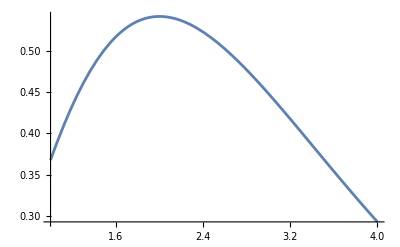

```mathematica
N[A,7] (*This provides 7 significant figures*)
Plot[g,{x,1,4}]
```

```mathematica
k=1/A;
f=k*g;
Integrate[f,{x,1,4}]
```

1

```mathematica
EV=Integrate[x*f,{x,1,4}]
EV//N (*This is another example of code to obtain a numerical approximation.Typing N[EV] gives the same result.*)
Var=Integrate[(x-EV)^2*f,{x,1,4}]
Var//N
```

```mathematica
EV=Integrate[x*f,{x,1,4}]
```

(2 (-71+8 ⅇ^3))/(-26+5 ⅇ^3)

```mathematica
EV//N
```

2.40997

```mathematica
Var=Integrate[(x-EV)^2*f,{x,1,4}]
```

(3 (420-422 ⅇ^3+23 ⅇ^6))/((26-5 ⅇ^3)^2)

```mathematica
Var//N
```

0.66221

```mathematica
Integrate[f,{x,1,3}]
%//N
```

(ⅇ (-17+5 ⅇ^2))/(-26+5 ⅇ^3)

0.728451

```mathematica
Integrate[f,{x,0,3}]
%//N
```

(ⅇ (-17+2 ⅇ^3))/(-26+5 ⅇ^3)

0.846265

```mathematica
Integrate[f,{x,2,3}]
%//N
```

(ⅇ (-17+10 ⅇ))/(-26+5 ⅇ^3)

0.371902

```mathematica
Integrate[f,{x,1,x}]
```

(5 ⅇ^3-ⅇ^(4-x) (2+x (2+x)))/(-26+5 ⅇ^3)

```mathematica
%//N
```

0.0134359 (100.428-1. 2.71828^(4.-1. x) (2.+x (2.+x)))

```mathematica
D[F,x]
```

0

```mathematica
F=Integrate[f,{x,1,x}] (*Make the right bound x,rather than a number*)
```

(5 ⅇ^3-ⅇ^(4-x) (2+x (2+x)))/(-26+5 ⅇ^3)

```mathematica
D[F,x]
```

(-ⅇ^(4-x) (2+2 x)+ⅇ^(4-x) (2+x (2+x)))/(-26+5 ⅇ^3)

```mathematica
f
```

(ⅇ^(4-x) x^2)/(-26+5 ⅇ^3)

```mathematica
f-D[F,x]//FullSimplify
```

0